```mathematica
ClearAll[files, importfile, raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/344/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/344/344.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/344/~$Книга1.xlsx}

```mathematica
importfile = files⟦2⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/344/344.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

```mathematica
dataset1=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset2 = makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
Range[-10000,10000,1000]
```

{-10000,-9000,-8000,-7000,-6000,-5000,-4000,-3000,-2000,-1000,0,1000,2000,3000,4000,5000,6000,7000,8000,9000,10000}

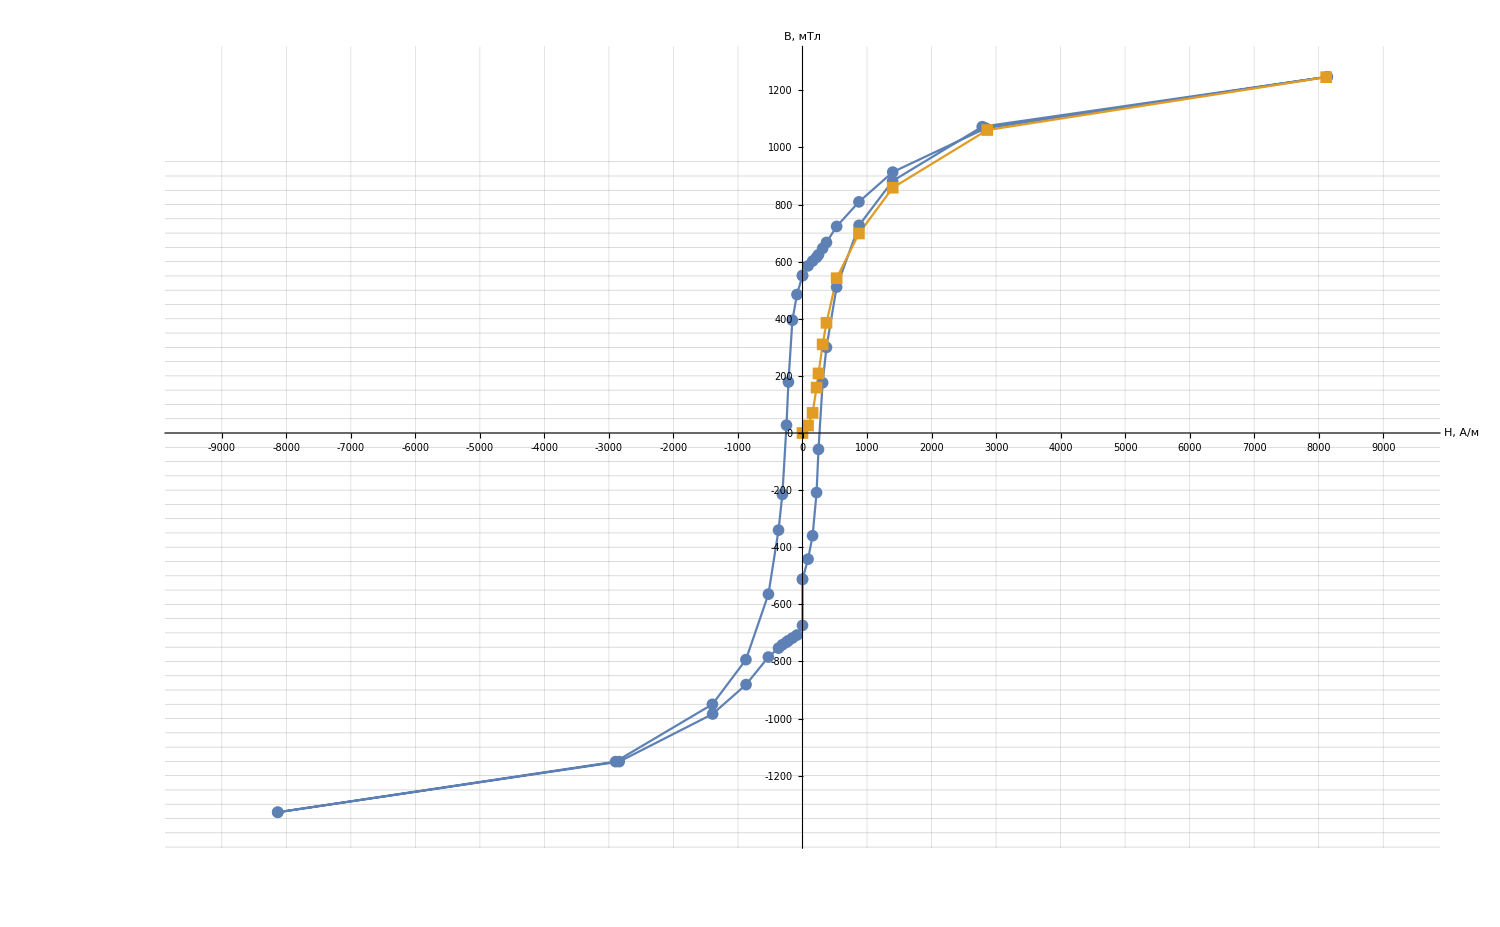

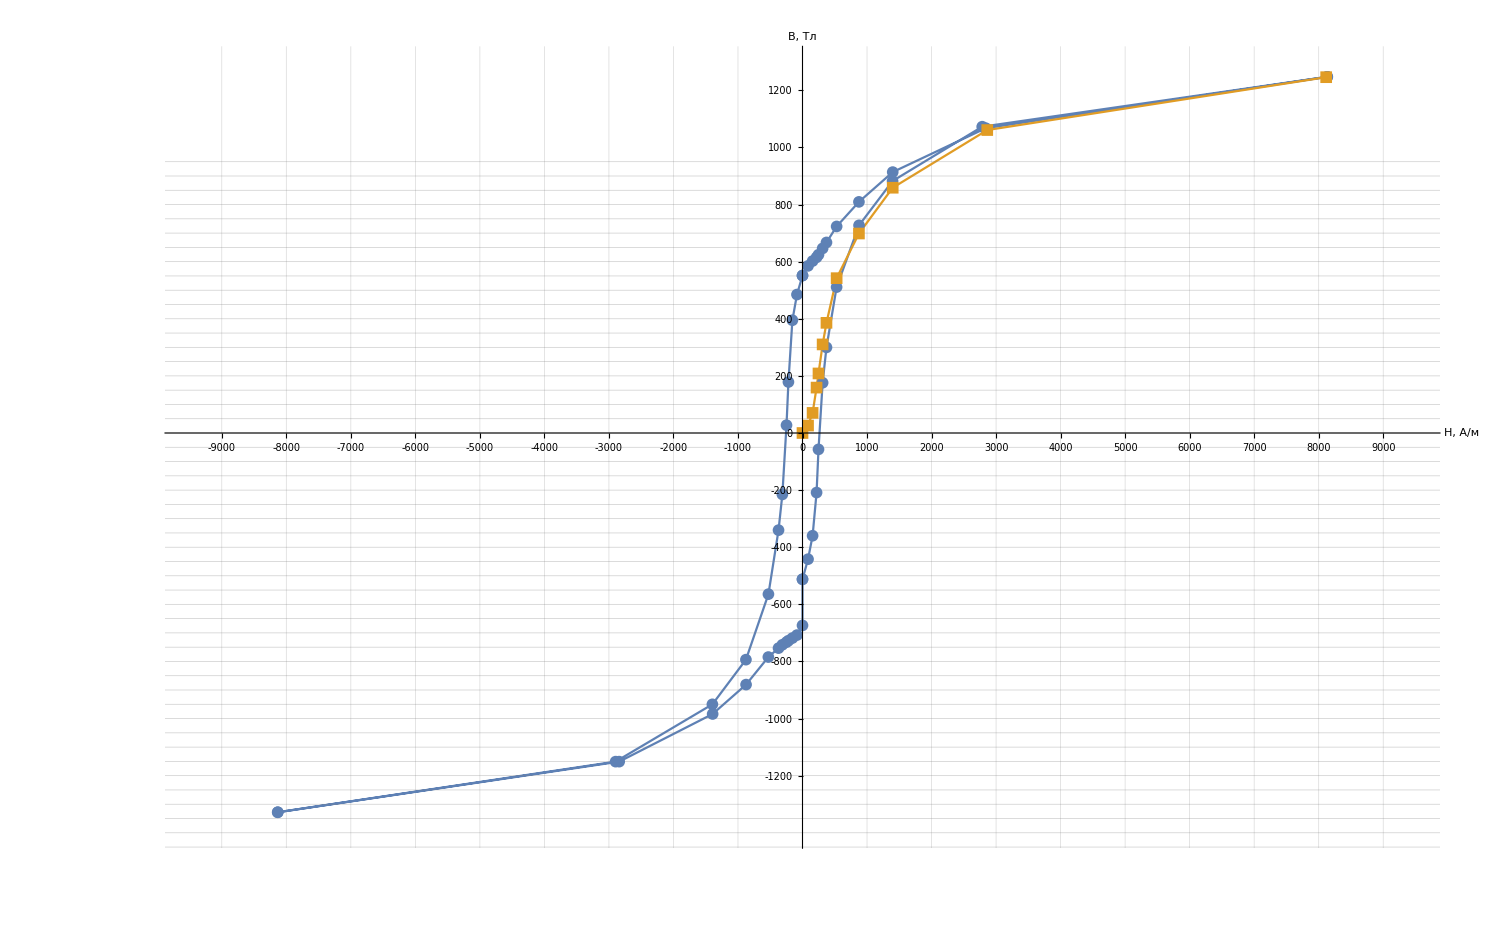

```mathematica
Show[
ListPlot[
{dataset1,dataset2},
Ticks-> {Range[-9000,9000,1000],Range[-1200,1200,200]},
TicksStyle->Directive[Black,14],
Joined->True,
PlotMarkers->{Automatic,12},
AxesLabel->{Style["H, А/м",Large],Style["В, мТл",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
PlotRange->{{-9500,9500},{-1400,1300}},
GridLines->{Range[-10000,10000,200], Range[-1500,1500,50]},
LabelStyle->Black
]
]
```

```mathematica
Show[%294,AxesStyle->Black]
```

```mathematica
Show[%292,AxesStyle->Black]
```

```mathematica
ClearAll[line,eq,x,data]
```

```mathematica
data = Normal@dataset2[All,{"H","B"}/*Values]
```

{{0.,0.},{85.7843,26.0669},{156.529,70.3806},{218.082,159.008},{247.883,208.535},{311.943,310.196},{371.546,385.79},{529.189,542.191},{874.554,698.593},{1398.17,858.904},{2863.19,1060.92},{8116.09,1246.}}

```mathematica
model =a+b/(x^d+c)
```

a+b/(c+x^d)

```mathematica
b/(c+x)
```

```mathematica
model= a+x^(1/15)
```

a+x^(1/15)

```mathematica
myfit = FindFit[data,model,{a,b,c,d},x]
```

{a→1.,b→1.,c→1.,d→1.}

```mathematica
modelf=Function[{x},Evaluate[model/.myfit]]
```

Function[{x},1.+1./(1.+x^1.)]

```mathematica
Aprox = LinearModelFit[data,{1,x,x^2},x]
```

FittedModel[100.286+0.539086 x-0.0000492788 x^2]

```mathematica
graph = Normal@Aprox
```

100.286+0.539086 x-0.0000492788 x^2

```mathematica
Approx = NonlinearModelFit[data,model,{a,b,c,d},x]
```

FittedModel[1.+1./(1.+x^1.)]

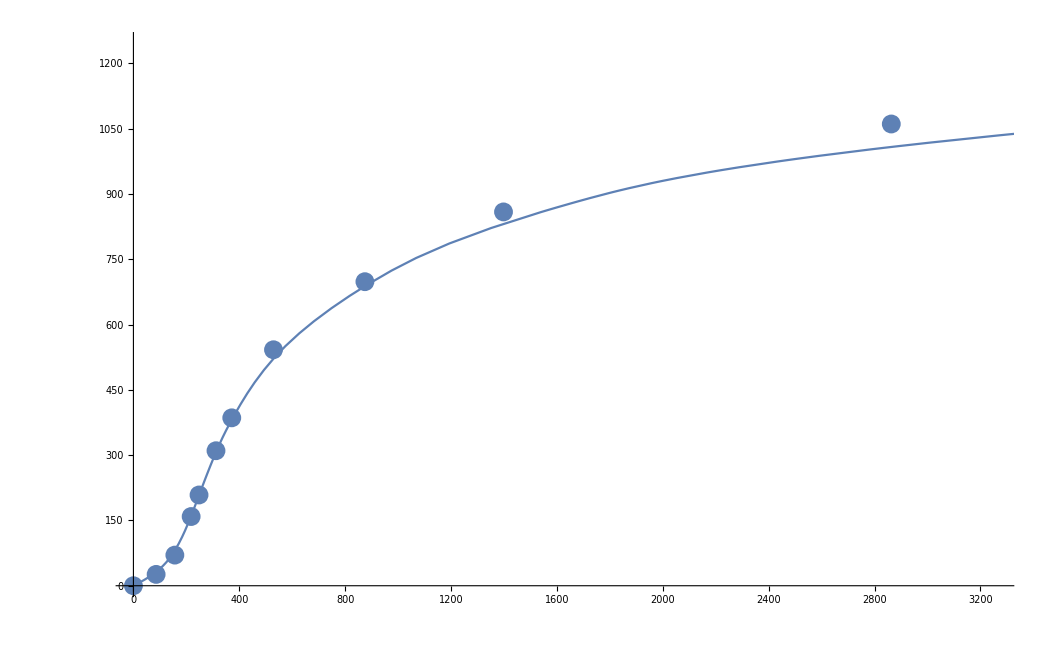

```mathematica
fit=BSplineFunction[data];
Show[ListPlot@data,ParametricPlot[fit@x,{x,0,1}],ImageSize->Large]
```

```mathematica
diffData=Reap[ParametricPlot[fit@t,{t,0,1},EvaluationMonitor:>Sow@fit@t]]⟦-1,1⟧;
```

```mathematica
diffF=Compile[{{arr,_Real,2}},MapThread[{(#1⟦1⟧+#2⟦1⟧)/2,(#2⟦2⟧-#1⟦2⟧)/(#2⟦1⟧-#1⟦1⟧)}&,{arr⟦;;-2⟧,arr⟦2;;⟧}]];
```

```mathematica
MaximalBy[diffF@diffData,Last]
```

{{246.756,1.6171}}

```mathematica
ClearAll@vecD
```

```mathematica
vecD[parametricF_,n_Integer][t_]:=With[{x0=parametricF[t]⟦1⟧,dx0=parametricF'[t]⟦1⟧},
Nest[f↦Echo[Print@f;{x0,If[MatchQ[f,_BSplineFunction],f'[#]⟦2⟧,Block[{$t},D[f⟦All,2⟧@$t,$t]/.$t->#]]/dx0}&],parametricF,n]@t
]
```

```mathematica
vecD[fit,2][0.5]
```

BSplineFunction[…]

```mathematica
deriv[2][fit_][t_]:=With[{first=fit',second=fit''},
{fit[t]⟦1⟧,(second[t]⟦2⟧first[t]⟦1⟧-second[t]⟦1⟧first[t]⟦2⟧)/(first[t]⟦1⟧^3)}
];
```

```mathematica
deriv[1][fit_][t_]:=With[{first=fit'},
{fit[t]⟦1⟧,(first[t]⟦2⟧)/(first[t]⟦1⟧)}
]
```

```mathematica
deriv[1][fit][x]
```

{x,(BSplineFunction[…][x]⟦2⟧)/x}

```mathematica
u[x_]:=deriv[1][fit][x]⟦2⟧
```

```mathematica
BS
```

```mathematica
NMaxValue[Unevaluated@{u[x],100<x<1000},x]
```

NMaxValue[Unevaluated[{u[x],100<x<1000}],x]

```mathematica
Unprotect@NMaximize
```

{NMaximize}

```mathematica
SetAttributes[NMaximize,HoldAll]
```

```mathematica
Attributes@NMaximize
```

{HoldAll}

```mathematica
u@x_:=Exp@-x^2
```

```mathematica
NMaximize[{u@x,10<x<100},x]
```

{3.72×10^-44,{x→10.}}